(32 √(ArcCos[1-(2 x)/125]-1/2 Sin[2 ArcCos[1-(2 x)/125]]))/(√π)

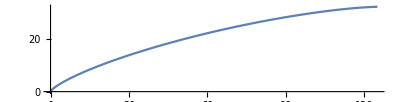

rocket-cone-125ld64.csv

-Graphics3D-

```mathematica
(* This program turns a curve describing the outline of a haack rocket cone into a csv file containing sampled points on the curve in unit: [cm] *)
c=0 (* Von Karman cone *);
l=125 (* Total length in mm*);
d=64 (* Diameter of base in mm*);
step=0.5;

r=d/2;
theta[x_]:=ArcCos[1-(2 x)/l];
y[x_]=(r Sqrt[theta[x]-Sin[2 theta[x] ]/2+c (Sin[theta[x]])^3])/Sqrt[Pi]
Plot[y[x],{x,0,l},PlotRange->Full,AspectRatio->(r/l)]
lstexport={};
xcoord=Table[x,{x,0,l,step}];
ycoord=Map[y,xcoord];
For[i=1,i≤Length[xcoord],i++,
AppendTo[lstexport,List[Part[xcoord,i]/10,Part[ycoord,i]/10,0]]
]
lstexport;
Export["rocket-cone-125ld64.csv",lstexport,"csv"]
RevolutionPlot3D[y[x],{x,0,1000},RevolutionAxis->{1,0,0}]
```

```mathematica
ClearAll["Global'*"]
```

```mathematica
RevolutionPlot3D[y[x],{x,0,1000},RevolutionAxis->{1,0,0}]
```

-Graphics3D-